101

Analysis done!

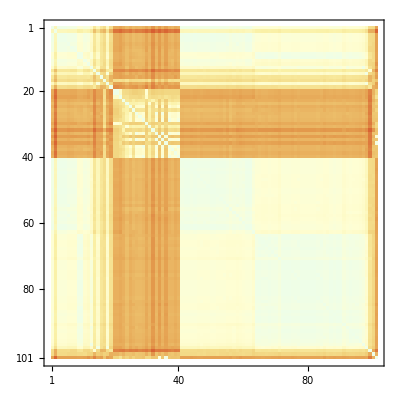

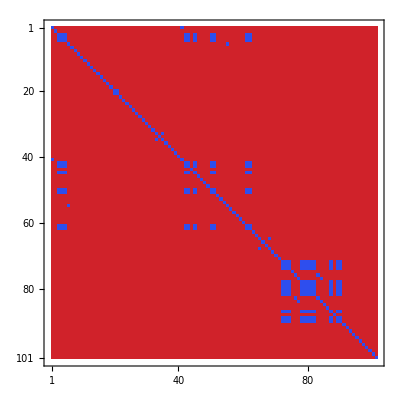

32

Ictalurus punctatus CTD

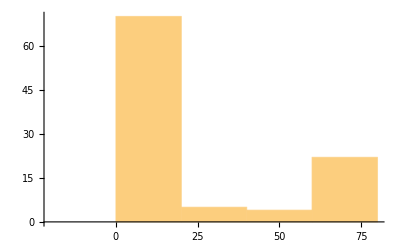

-Graphics-

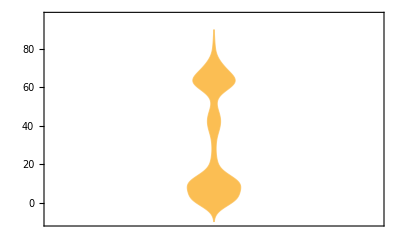

Average Edit Distance: 31.6818 +/- 27.0856

Median Edit Distance: 16. +/- 15.

CTD_DistributionGraph.pdf

```mathematica
(* Provide input file path *)

Datei="Unique species CTDs.fasta";

Sequenzen=Import[Datei,"Sequence"];
Header=Import[Datei,"Header"];
Length[Header]

Distances={};
Do[{a1=Sequenzen[[a]],
temp={};
Do[{b1=Sequenzen[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Sequenzen]}],
Distances=AppendTo[Distances,temp]
},{a,1,Length[Sequenzen]}]
Print[Style["Analysis done!",Bold,Blue]]



(* Plot the data *)

MatrixPlot[Distances,ColorFunction->"LightTemperatureMap"]
MatrixPlot[Distances,ColorFunction->"TemperatureMap",ColorFunctionScaling->False]

pos=Flatten[Position[Distances[[1]],Max[Distances[[1]]]]][[1]]
Header[[pos]]

Histogram[Distances[[1]]]
Histogram[Distances[[1]]]
ExpGraphik=DistributionChart[{0,Flatten[Distances],0},
PlotRange->{{1,6},{Automatic,98}}]

UbDistances=Flatten[Distances];

Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[UbDistances]]," +/- ",
N[StandardDeviation[UbDistances]]]

Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[UbDistances]]," +/- ",
N[MedianDeviation[UbDistances]]]


SetDirectory[DirectoryName[Datei]];
Export["CTD_DistributionGraph.pdf",ExpGraphik]
```

Ailuropoda melanoleuca CTD | 1
Alligator sinensis CTD | 1
Amazona aestiva CTD | 1
Apaloderma vittatum CTD | 1
Aptenodytes forsteri CTD | 1
Apteryx australis mantelli CTD | 1
Balaenoptera acutorostrata scammoni CTD | 1
Bos taurus CTD | 1
Callithrix jacchus CTD | 1
Calypte anna CTD | 1
Caprimulgus carolinensis CTD | 1
Cariama cristata CTD | 1
Cercocebus atys CTD | 1
Chaetura pelagica CTD | 1
Charadrius vociferus CTD | 1
Chlamydotis macqueenii CTD | 1
Chrysemys picta bellii CTD | 1
Chrysochloris asiatica CTD | 1
Condylura cristata CTD | 1
Corvus cornix cornix CTD | 1
Cuculus canorus CTD | 1
Dasypus novemcinctus CTD | 1
Elephantulus edwardii CTD | 1
Equus caballus CTD | 1
Erinaceus europaeus CTD | 1
Eurypyga helias CTD | 1
Falco peregrinus CTD | 1
Felis catus CTD | 1
Ficedula albicollis CTD | 1
Gallus gallus CTD | 1
Heterocephalus glaber CTD | 1
Homo sapiens CTD | 1
Jaculus jaculus CTD | 1
Lepidothrix coronata CTD | 1
Loxodonta africana CTD | 1
Meleagris gallopavo CTD | 1
Melopsittacus undulatus CTD | 1
Microcebus murinus CTD | 1
Miniopterus natalensis CTD | 1
Mus musculus CTD | 1
Myotis lucifugus CTD | 1
Nestor notabilis CTD | 1
Nomascus leucogenys CTD | 1
Octodon degus CTD | 1
Ophiophagus hannah CTD | 1
Opisthocomus hoazin CTD | 1
Ornithorhynchus anatinus CTD | 1
Orycteropus afer afer CTD | 1
Ovis aries CTD | 1
Ovis aries musimon CTD | 1
Pantholops hodgsonii CTD | 1
Pelecanus crispus CTD | 1
Pelodiscus sinensis CTD | 1
Phaethon lepturus CTD | 1
Phoenicopterus ruber ruber CTD | 1
Picoides pubescens CTD | 1
Pongo abelii CTD | 1
Pseudopodoces humilis CTD | 1
Pterocles gutturalis CTD | 1
Pteropus alecto CTD | 1
Pygoscelis adeliae CTD | 1
Python bivittatus CTD | 1
Sarcophilus harrisii CTD | 1
Sorex araneus CTD | 1
Struthio camelus australis CTD | 1
Sturnus vulgaris CTD | 1
Sus scrofa CTD | 1
Taeniopygia guttata CTD | 1
Tauraco erythrolophus CTD | 1
Thamnophis sirtalis CTD | 1
Tinamus guttatus CTD | 1
Ursus maritimus CTD | 1
Zonotrichia albicollis CTD | 1
Anas platyrhynchos CTD | 2
Astyanax mexicanus CTD | 2
Austrofundulus limnaeus CTD | 2
Callorhinchus milii CTD | 2
Clupea harengus CTD | 2
Colius striatus CTD | 2
Columba livia CTD | 2
Cyprinodon variegatus CTD | 2
Esox lucius CTD | 2
Ictalurus punctatus CTD | 2
Kryptolebias marmoratus CTD | 2
Larimichthys crocea CTD | 2
Lepisosteus oculatus CTD | 2
Nothobranchius furzeri CTD | 2
Notothenia coriiceps CTD | 2
Oreochromis niloticus CTD | 2
Oryzias latipes CTD | 2
Poecilia formosa CTD | 2
Poecilia mexicana CTD | 2
Pundamilia nyererei CTD | 2
Pygocentrus nattereri CTD | 2
Salmo salar CTD | 2
Sinocyclocheilus anshuiensis CTD | 2
Sinocyclocheilus grahami CTD | 2
Sinocyclocheilus rhinocerous CTD | 2
Stegastes partitus CTD | 2
Xenopus laevis CTD | 2
Xiphophorus maculatus CTD | 2

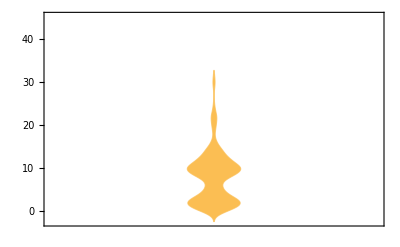

Average Edit Distance: 7.95646 +/- 6.13563

Median Edit Distance: 8. +/- 4.

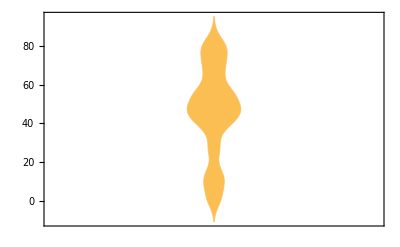

Average Edit Distance: 46.2041 +/- 22.8421

Median Edit Distance: 48. +/- 14.

```mathematica
(* Cluster analysis*)

TableForm[SortBy[Transpose[{Header,ClusteringComponents[Distances,2][[1]]}],Last]]
ClusterSeq=SortBy[Transpose[{Sequenzen,ClusteringComponents[Distances,2][[1]]}],Last];

(* Analyze sequences in cluster 1*)
TempCluster1=Select[ClusterSeq,#[[2]]==1&];
Cluster1=Transpose[TempCluster1][[1]];
Cl1dist={};
Do[{a1=Cluster1[[a]],
temp={};
Do[{b1=Cluster1[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Cluster1]}],
Cl1dist=AppendTo[Cl1dist,temp]
},{a,1,Length[Cluster1]}]
DistributionChart[{0,Flatten[Cl1dist],0},
PlotRange->{{1,6},{Automatic,40}}]
Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[Flatten[Cl1dist]]]," +/- ",
N[StandardDeviation[Flatten[Cl1dist]]]]
Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[Flatten[Cl1dist]]]," +/- ",
N[MedianDeviation[Flatten[Cl1dist]]]]

(* Analyze sequences in cluster 2*)
TempCluster2=Select[ClusterSeq,#[[2]]==2&];
Cluster2=Transpose[TempCluster2][[1]];
Cl2dist={};
Do[{a1=Cluster2[[a]],
temp={};
Do[{b1=Cluster2[[b]],
dist=EditDistance[a1,b1],
temp=AppendTo[temp,dist]
},{b,1,Length[Cluster2]}],
Cl2dist=AppendTo[Cl2dist,temp]
},{a,1,Length[Cluster2]}]
DistributionChart[{0,Flatten[Cl2dist],0},
PlotRange->{{1,6},{Automatic,40}}]
Print[Style["Average Edit Distance: ",Bold,Blue],
N[Mean[Flatten[Cl2dist]]]," +/- ",
N[StandardDeviation[Flatten[Cl2dist]]]]
Print[Style["Median Edit Distance: ",Bold,Blue],
N[Median[Flatten[Cl2dist]]]," +/- ",
N[MedianDeviation[Flatten[Cl2dist]]]]
```